g2 tadpole computation.
Dependencies: ModCatFunctions (NCAlgebra)

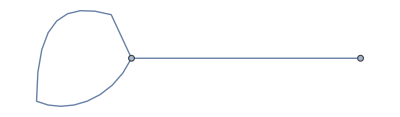

```mathematica
graph = { {0,1},{1, 1} };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[alph, beta, gamm];
SetNonCommutative[alph, beta, gamm];
BGamma = { {0,alph},{beta, gamm} };
q=Exp[2*Pi*I/30];(* 2*Pi*I/(3*(4+ level)) *)
```

```mathematica
SetDirectory["/Users/calebhill/Documents/UNH/Research/code/gen2"];
Export["regularLowOrder_14.txt", regularLowOrderEqns];
```

To do next: make Mathematica change, e.g., Sqrt[..] to sqrt(..)

```mathematica
FindInstance[lowOrderEqns,alpha, Reals, 2]
```

{{alpha1→-1,alpha2→-1,alpha3→1/2 (-1+√5),alpha4→-√(1/2 (-1+√5))},{alpha1→1,alpha2→1,alpha3→1/2 (1-√5),alpha4→√(1/2 (-1+√5))}}